# Lesson 1

## Arithmetic

```mathematica
1+2
```

3

```mathematica
3*6
```

18

```mathematica
3 6(* space *)
```

18

```mathematica
4^2
```

16

```mathematica
4^2(* ctrl + 6 *)
```

16

```mathematica
5!
```

120

```mathematica
Sin[30 Degree]
```

1/2

```mathematica
Log[E]
```

1

```mathematica
Log[ⅇ](* esc ee esc *)
```

1

```mathematica
Pi==π
```

True

```mathematica
ⅇ^(π ⅈ)(* esc ii esc *)
```

-1

## Functions

```mathematica
f[x_]:=Cos[x]+Sin[x]
```

```mathematica
f[π/3]
```

1/2+(√3)/2

```mathematica
f@f@π
```

Cos[1]-Sin[1]

```mathematica
π//f
```

-1

```mathematica
g[i_Integer]:=2^i
```

```mathematica
g[3]
```

8

```mathematica
g[3.14]
```

g[3.14]

```mathematica
Out[17]
```

-1

```mathematica
h[x_,y_]:=Cos[x]Sin[y]
```

```mathematica
Exp[{x,π,ⅈ}]
```

{ⅇ^x,ⅇ^π,ⅇ^ⅈ}

```mathematica
g[{1,2,3}]
```

g[{1,2,3}]

```mathematica
SetAttributes[g,Listable]
```

```mathematica
g[{1,2,3}](*{g[1],g[2],g[3]}*)
```

{2,4,8}

```mathematica
Map[g,{i,j,k}]
g/@{i,j,k}
```

{g[i],g[j],g[k]}

{g[i],g[j],g[k]}

## Expressions

```mathematica
x^3+2x+1
```

1+2 x+x^3

```mathematica
y=%
```

1+2 x+x^3

```mathematica
y
```

1+2 x+x^3

```mathematica
y/.x->a+b(* esc -> esc *)
```

1+2 (a+b)+(a+b)^3

```mathematica
Expand[y/.x->a+b]
```

1+2 a+a^3+2 b+3 a^2 b+3 a b^2+b^3

```mathematica
x=1
```

1

```mathematica
y
```

4

```mathematica
Unset@x(* x = .*)
```

```mathematica
y
```

1+2 x+x^3

```mathematica
y[t]
```

y[t]

```mathematica
D[y[t],t]
```

y'[t]

```mathematica
D[y[t],{t,2}]/.y->Cos
```

-Cos[t]

## Lists Vector Operations

```mathematica
{1,ⅉ,π,x+y,"STRING", f,f[π]}(* esc jj esc *)
```

{1,ⅈ,π,1+3 x+x^3,STRING,f,-1}

```mathematica
X={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]};
y=.
Y={Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]};
```

```mathematica
X+Y
```

{x_1+y_1,x_2+y_2,x_3+y_3}

```mathematica
X Y
```

{x_1 y_1,x_2 y_2,x_3 y_3}

```mathematica
X.Y
```

x_1 y_1+x_2 y_2+x_3 y_3

```mathematica
X×Y
```

{-x_3 y_2+x_2 y_3,x_3 y_1-x_1 y_3,-x_2 y_1+x_1 y_2}

```mathematica
X⊗Y
```

{{x_1 y_1,x_1 y_2,x_1 y_3},{x_2 y_1,x_2 y_2,x_2 y_3},{x_3 y_1,x_3 y_2,x_3 y_3}}

```mathematica
%//MatrixForm
```

(x_1 y_1 | x_1 y_2 | x_1 y_3
x_2 y_1 | x_2 y_2 | x_2 y_3
x_3 y_1 | x_3 y_2 | x_3 y_3)

## Heads

```mathematica
Head@x
```

Symbol

```mathematica
Head@1
```

Integer

```mathematica
Head[1+ⅈ]
```

Complex

```mathematica
Head[{1,2,3}]
```

List

```mathematica
Head[x+y]
```

Plus

```mathematica
Plus[x,y]
```

x+y

```mathematica
Head[Cos[x]]
```

Cos

```mathematica
Head@{x,y}
```

List

```mathematica
Plus@@{x,y}
```

x+y

```mathematica
{x,y}==List[x,y]
```

True

```mathematica
h[π/3,π/6]
```

1/4

```mathematica
h[{π/3,π/6}]
```

h[{π/3,π/6}]

```mathematica
h[Sequence@@{x,y}](* h[x,y] *)
```

Cos[x] Sin[y]

## Definitions

```mathematica
?x
```

```mathematica
?f
```

```mathematica
?g
```

```mathematica
Clear[g]
```

```mathematica
g[1]
```

g[1]

```mathematica
?g
```

```mathematica
g[{1,2,3}]
```

{g[1],g[2],g[3]}

```mathematica
ClearAll[g]
```

```mathematica
?g
```

```mathematica
Remove@x
```

```mathematica
?x
```

Missing[UnknownSymbol,x]

```mathematica
x
```

x

```mathematica
?x
```

## Plots

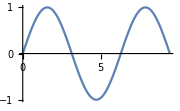

```mathematica
Plot[Sin[x],{x,0,3π}
,ImageSize->Small]
```

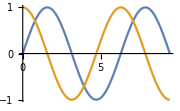

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,3π}
,ImageSize->Small]
```

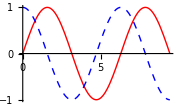

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,3π}
,ImageSize->Small
,PlotStyle->{{Red,Thick},{Blue,Thin,Dashed}}]
```

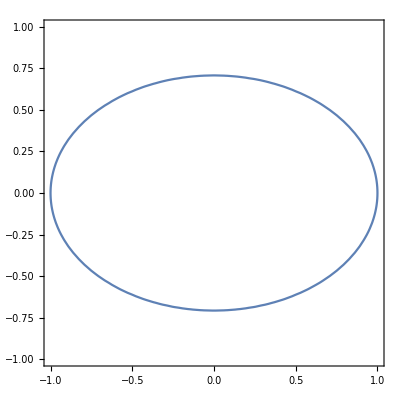

```mathematica
ContourPlot[x^2+2 y^2==1,{x,-1,1},{y,-1,1}
,ImageSize->Tiny]
```

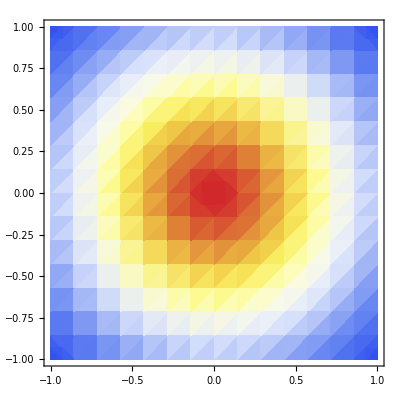

```mathematica
DensityPlot[ⅇ^(-x^2-y^2),{x,-1,1},{y,-1,1}
,ImageSize->Tiny
,ColorFunction->"TemperatureMap"]
```

```mathematica
ColorData["Named"]
```

{Atoms,Crayola,GeologicAges,HTML,Legacy,WebSafe}

```mathematica
ColorData["Atoms","ColorList"]
```

{RGBColor[0.65, 0.7, 0.7],RGBColor[0.836713, 1., 1.],RGBColor[0.799435, 0.543572, 0.997559],RGBColor[0.770565, 0.964309, 0.0442359],RGBColor[1., 0.709804, 0.709804],RGBColor[0.4, 0.4, 0.4],RGBColor[0.291989, 0.437977, 0.888609],RGBColor[0.800498, 0.201504, 0.192061],RGBColor[0.578462, 0.85539, 0.408855],RGBColor[0.677263, 0.928423, 0.955287],RGBColor[0.658708, 0.492173, 0.842842],RGBColor[0.628274, 0.850553, 0.0782731],RGBColor[0.8913, 0.631904, 0.627399],RGBColor[0.941176, 0.784314, 0.627451],RGBColor[1., 0.501961, 0],RGBColor[0.90443, 0.97015, 0.13504],RGBColor[0.412698, 0.932689, 0.166398],RGBColor[0.546138, 0.844244, 0.892092],RGBColor[0.534026, 0.420729, 0.705621],RGBColor[0.480072, 0.744591, 0.0955222],RGBColor[0.901961, 0.901961, 0.901961],RGBColor[0.74902, 0.760784, 0.780392],RGBColor[0.65098, 0.65098, 0.670588],RGBColor[0.541176, 0.6, 0.780392],RGBColor[0.611765, 0.478431, 0.780392],RGBColor[0.878431, 0.4, 0.2],RGBColor[0.941176, 0.564706, 0.627451],RGBColor[0.313725, 0.815686, 0.313725],RGBColor[0.784314, 0.501961, 0.2],RGBColor[0.490196, 0.501961, 0.690196],RGBColor[0.800757, 0.542666, 0.533513],RGBColor[0.60508, 0.632465, 0.576489],RGBColor[0.741176, 0.501961, 0.890196],RGBColor[0.917248, 0.657833, 0.0706628],RGBColor[0.58847, 0.22163, 0.16064],RGBColor[0.426019, 0.747462, 0.810413],RGBColor[0.425391, 0.329242, 0.585895],RGBColor[0.325959, 0.646423, 0.095983],RGBColor[0.531014, 1., 1.],RGBColor[0.458599, 0.917466, 0.918573],RGBColor[0.385036, 0.834854, 0.841681],RGBColor[0.310325, 0.752163, 0.769323],RGBColor[0.234466, 0.669394, 0.701499],RGBColor[0.157459, 0.586546, 0.638209],RGBColor[0.0793033, 0.50362, 0.579453],RGBColor[0., 0.420615, 0.525231],RGBColor[0.752941, 0.752941, 0.752941],RGBColor[1., 0.85098, 0.560784],RGBColor[0.728371, 0.440594, 0.422196],RGBColor[0.39799, 0.491477, 0.495586],RGBColor[0.619608, 0.388235, 0.709804],RGBColor[0.816706, 0.451332, 0.0100947],RGBColor[0.580392, 0, 0.580392],RGBColor[0.316906, 0.638078, 0.710252],RGBColor[0.332803, 0.217712, 0.483666],RGBColor[0.165935, 0.55605, 0.0796556],RGBColor[0.928084, 0.716075, 0.329427],RGBColor[0.894824, 0.731424, 0.325131],RGBColor[0.86523, 0.707999, 0.315261],RGBColor[0.837836, 0.662974, 0.301635],RGBColor[0.811992, 0.607859, 0.285626],RGBColor[0.787563, 0.549894, 0.268279],RGBColor[0.764628, 0.493261, 0.250405],RGBColor[0.743177, 0.440115, 0.23269],RGBColor[0.72281, 0.39143, 0.215783],RGBColor[0.702434, 0.347663, 0.200392],RGBColor[0.679962, 0.309234, 0.187368],RGBColor[0.652012, 0.276823, 0.17779],RGBColor[0.613603, 0.251489, 0.173042],RGBColor[0.557855, 0.234598, 0.17489],RGBColor[0.475685, 0.227573, 0.18555],RGBColor[0.781537, 0.717388, 0.716579],RGBColor[0.734443, 0.544489, 0.683471],RGBColor[0.681179, 0.360409, 0.63675],RGBColor[0.605181, 0.367584, 0.556343],RGBColor[0.521806, 0.382125, 0.469204],RGBColor[0.445624, 0.373159, 0.399069],RGBColor[0.815686, 0.815686, 0.878431],RGBColor[1., 0.819608, 0.137255],RGBColor[0.721569, 0.721569, 0.815686],RGBColor[0.65098, 0.329412, 0.301961],RGBColor[0.341176, 0.34902, 0.380392],RGBColor[0.619608, 0.309804, 0.709804],RGBColor[0.670588, 0.360784, 0],RGBColor[0.458824, 0.309804, 0.270588],RGBColor[0.218799, 0.516091, 0.591608],RGBColor[0.25626, 0.0861372, 0.398932],RGBColor[0., 0.473472, 0.04654],RGBColor[0.322042, 0.71693, 0.988479],RGBColor[0.3608, 0.67166, 0.943003],RGBColor[0.397469, 0.628, 0.898853],RGBColor[0.43205, 0.58595, 0.856029],RGBColor[0.464542, 0.54551, 0.814532],RGBColor[0.494945, 0.506679, 0.774361],RGBColor[0.52326, 0.469458, 0.735517],RGBColor[0.549486, 0.433847, 0.697999],RGBColor[0.573624, 0.399845, 0.661808],RGBColor[0.595673, 0.367454, 0.626942],RGBColor[0.615633, 0.336672, 0.593404],RGBColor[0.633505, 0.307499, 0.561191],RGBColor[0.649288, 0.279937, 0.530305],RGBColor[0.662982, 0.253984, 0.500746],RGBColor[0.674588, 0.22964, 0.472513],RGBColor[0.684106, 0.206907, 0.445606],RGBColor[0.691534, 0.185783, 0.420025],RGBColor[0.696874, 0.166269, 0.395772],RGBColor[0.700126, 0.148365, 0.372844],RGBColor[0.701289, 0.13207, 0.351243],RGBColor[0.700363, 0.117385, 0.330968],RGBColor[0.697348, 0.10431, 0.31202],RGBColor[0.692245, 0.0928444, 0.294398],RGBColor[0.685054, 0.0829886, 0.278102],RGBColor[0.675773, 0.0747426, 0.263133],RGBColor[0.664405, 0.0681063, 0.249491],RGBColor[0.650947, 0.0630797, 0.237174],RGBColor[0.635401, 0.0596628, 0.226184],RGBColor[0.635401, 0.056628, 0.226184],RGBColor[0.635401, 0.0528, 0.226184]}

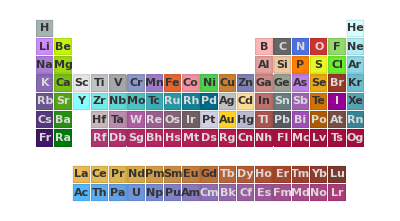

```mathematica
ColorData["Atoms","Panel"]
```

```mathematica
RGBColor[0.721569, 0.721569, 0.815686]
```

```mathematica
RGBColor[1,0.8,0.13]
```

RGBColor[1, 0.8, 0.13]

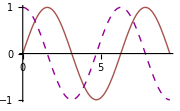

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,3π}
,ImageSize->Small
,PlotStyle->{{RGBColor[0.65098, 0.329412, 0.301961],Thick},{RGBColor[0.580392, 0, 0.580392],Thin,Dashed}}]
```

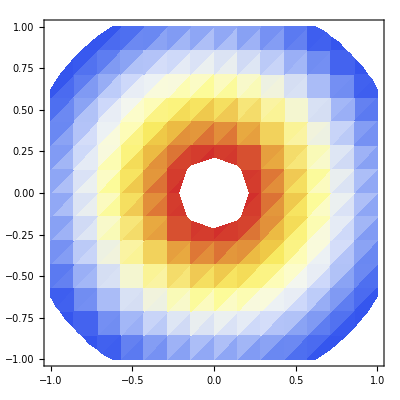

```mathematica
DensityPlot[ⅇ^(-x^2-y^2),{x,-1,1},{y,-1,1}
,ImageSize->Tiny
,ColorFunction->"TemperatureMap"
,PlotRange->{All,All,{0.25,0.95}}]
```

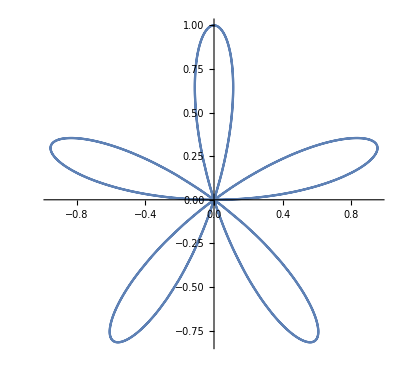

```mathematica
PolarPlot[Sin[5ϕ],{ϕ,0,2π},ImageSize->Tiny]
```

```mathematica
Manipulate[
PolarPlot[Sin[n (ϕ-α)],{ϕ,0,2π},ImageSize->Tiny],
{n,2,8,1},{α,0,2π}]
```

```mathematica
Manipulate[
PolarPlot[Sin[n (ϕ-α)],{ϕ,0,2π}
,ImageSize->Tiny
,PlotRange->{{-1,1},{-1,1}}],
{n,2,8,1},{α,0,2π}
,ContentSize->Tiny
,Paneled->False
,Alignment->Center]
```